## Level-set 2D

```mathematica
Clear["Global`*"]
```

#### stiffnessMatrix

```mathematica
stiffnessMatrix[k_List]:=
{
{k[[1]],k[[2]],k[[3]],k[[4]],k[[5]],k[[6]],k[[7]],k[[8]]},
{k[[2]],k[[1]],k[[8]],k[[7]],k[[6]],k[[5]],k[[4]],k[[3]]},
{k[[3]],k[[8]],k[[1]],k[[6]],k[[7]],k[[4]],k[[5]],k[[2]]},
{k[[4]],k[[7]],k[[6]],k[[1]],k[[8]],k[[3]],k[[2]],k[[5]]},
{k[[5]],k[[6]],k[[7]],k[[8]],k[[1]],k[[2]],k[[3]],k[[4]]},
{k[[6]],k[[5]],k[[4]],k[[3]],k[[2]],k[[1]],k[[8]],k[[7]]},
{k[[7]],k[[4]],k[[5]],k[[2]],k[[3]],k[[8]],k[[1]],k[[6]]},
{k[[8]],k[[3]],k[[2]],k[[5]],k[[4]],k[[7]],k[[6]],k[[1]]}
}
```

#### matInfo

```mathematica
materialInfo:=Block[
{ym,pr,λ,μ,KE,KTr,k},
ym=1.;
pr=0.3;
λ=ym*pr/((1+pr)*(1-pr));
μ=ym/2/(1+pr);
(*stiffness matrix ke*)
k={1/2-pr/6,1/8+pr/8,-1/4-pr/12,-1/8+3*pr/8,-1/4+pr/12,-1/8-pr/8,pr/6,1/8-3pr/8};
KE=ym/(1-pr^2)*stiffnessMatrix[k];
k={1/3,1/4,-1/3,1/4,-1/6,-1/4,1/6,-1/4};
KTr=ym/(1-pr)*stiffnessMatrix[k];
{KE,KTr,λ,μ}
]
```

#### FE

```mathematica
FE[struc_,KE_]:=Block[
{str=struc,ke=KE,nely,nelx,K,F,U,elx,ely,n1,n2,edof,fixeddofs,alldofs,freedofs,posTdof,i},
{nely,nelx}=Dimensions[str];

K=ConstantArray[0.,{2*(nelx+1)*(nely+1),2*(nelx+1)*(nely+1)}];
F=ConstantArray[0.,{2*(nelx+1)*(nely+1),1}];
U=ConstantArray[0.,{2*(nelx+1)*(nely+1),1}];

For[elx=1,elx≤nelx,elx++,
For[ely=1,ely≤nely,ely++,

n1=(nely+1)*(elx-1)+ely;
n2=(nely+1)*elx+ely;
edof={2n1-1,2n1,2n2-1,2n2,2n2+1,2n2+2,2n1+1,2n1+2};
K[[edof,edof]]=K[[edof,edof]]+Max[str[[ely,elx]],0.001]*ke;

];
];

posTdof[x_Integer,y_Integer]:={2*((nely+1)*x+y+1)-1,2*((nely+1)*x+y+1)};

(*F[[2*(Round[nelx/2]+1)*(nely+1)]]={1.};*)
(*F[[2*(nelx+1)*(nely+1)]]={1.};*)
(*For[i=0,i≤nelx,i++,
F[[posTdof[i,0][[2]]]]={(i)^2/(nelx)^2};
];*)
F[[posTdof[nelx,nely/2][[2]]]]={1};
(*fixeddofs=Flatten@{
Range[2*(nely+1)-1,2*(nely+1)]
,
Range[2*(nelx+1)*(nely+1)-1,2*(nelx+1)*(nely+1)]
};*)
(*fixeddofs=Flatten@{
Range[1,2*(nely+1)]
};*)
fixeddofs=Flatten@{
posTdof[0,0],posTdof[0,nely]
};

alldofs=Range[1,2*(nely+1)*(nelx+1)];
freedofs=Complement[alldofs,fixeddofs];
U[[freedofs]]=LinearSolve[K[[freedofs,freedofs]],F[[freedofs]]];
U

]
```

#### evolve

```mathematica
evolve[v_,g_,lsf_,stepLength_,w_]:=Block[
{vFull,gFull,dt,i,lsfup=lsf,dpx,dmx,dpy,dmy,strucFull,strucup},

vFull=ArrayPad[v,1];
gFull=ArrayPad[g,1];

(*Print[{"test",MatrixForm@(v)}];*)

dt=0.1/Max[Abs[Flatten[v]]];

For[i=1,i≤(stepLength*10),i++,
dpx=RotateRight[lsfup,{0,-1}]-lsfup;
dmx=lsfup-RotateRight[lsfup,{0,1}];
dpy=RotateRight[lsfup,{-1,0}]-lsfup;
dmy=lsfup-RotateRight[lsfup,{1,0}];

lsfup=lsfup-dt*Map[Min[#,0]&,vFull,{2}]*Sqrt[Map[Min[#,0]&,dmx,{2}]^2+Map[Max[#,0]&,dpx,{2}]^2+Map[Min[#,0]&,dmy,{2}]^2+Map[Max[#,0]&,dpy,{2}]^2]-dt*Map[Max[#,0]&,vFull,{2}]*Sqrt[Map[Max[#,0]&,dmx,{2}]^2+Map[Min[#,0]&,dpx,{2}]^2+Map[Max[#,0]&,dmy,{2}]^2+Map[Min[#,0]&,dpy,{2}]^2]-w*dt*gFull;
];

strucFull=Map[Boole[#<0]&,lsfup,{2}];
strucup=strucFull[[2;;-2,2;;-2]];
{strucup,lsfup}
]
```

```mathematica
Min[{{-1,1},{2,-2}},0]
```

-2

```mathematica
ls={{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
RotateRight[ls,{0,-1}]-ls
```

{{1,1,-2},{1,1,-2},{1,1,-2}}

#### bwdist

```mathematica
bwdist[Array_]:=ImageData[DistanceTransform[Image[Map[If[#==0,1,0]&,Array,{2}]], DistanceFunction->EuclideanDistance]]
```

#### updateStep

```mathematica
tt={{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
tt[[1]]
```

{1,2,3}

```mathematica
updateStep[lsF_,shapeS_,topS_,stepLength_,topWeight_]:=Block[
{shapeSens=shapeS,topSens=topS,lsf=lsF,l1,l2,l3,l4,struc},

shapeSens=ListConvolve[1/6*{{0,1,0},{1,2,1},{0,1,0}},ArrayPad[shapeSens,{1,1},"Fixed"]];
topSens=ListConvolve[1/6*{{0,1,0},{1,2,1},{0,1,0}},ArrayPad[topSens,{1,1},"Fixed"]];

(*Чувствительность вблизи зоны закрепления и приложения сил зануляем, вернуть при неправильной работе, сейчас вставлена*)
{l1,l2}=Dimensions[shapeSens];
{l3,l4}=Dimensions[topSens];
(*nely,nelx*)
shapeSens[[1,1]]=shapeSens[[l1,1]]=shapeSens[[l1/2,l2]]=0;
topSens[[1,1]]=topSens[[l1,1]]=topSens[[l1/2,l2]]=0;
{struc,lsf}=evolve[-shapeSens,topSens*Map[If[#<0,1,0]&,lsf[[2;;-2,2;;-2]],{2}],lsf,stepLength,topWeight]
]
```

#### reinit

```mathematica
reinit[struc_]:=Block[
{str=struc,strucFull},
strucFull=ArrayPad[str,1];
Map[If[#==0,1,0]&,strucFull,{2}]*(bwdist[strucFull]-0.5)-strucFull*(bwdist[strucFull-1]-0.5)
]
```

#### toplevelset

```mathematica
toplevelset[nelX_,nelY_,volReQ_,stepLengtH_,numReiniT_,topWeighT_]:=
Block[
{nelx=nelX,nely=nelY,volReq=volReQ,stepLength=stepLengtH,numReinit=numReiniT,topWeight=topWeighT,struc,lsf,shapeSens,topSens,KE,KTr,λ,μ,i,u,iterNum,elx,ely,n1,n2,ue,obj,volCurr,la,La,alpha,imageData,k},

imageData={};
struc=ConstantArray[1.,{nely,nelx}];
struc[[Round[nely/2]-1;;Round[nely/2]+1,Round[nelx/2]-1;;Round[nelx/2]+1]]=struc[[Round[nely/2]-1;;Round[nely/2]+1,Round[nelx/2]-1;;Round[nelx/2]+1]]*0;
struc[[Round[nely/2]-1;;Round[nely/2]+1,Round[nelx/3]-1;;Round[nelx/3]+1]]=struc[[Round[nely/2]-1;;Round[nely/2]+1,Round[nelx/3]-1;;Round[nelx/3]+1]]*0;
struc[[Round[nely/2]-1;;Round[nely/2]+1,Round[2nelx/3]-1;;Round[2nelx/3]+1]]=struc[[Round[nely/2]-1;;Round[nely/2]+1,Round[2nelx/3]-1;;Round[2nelx/3]+1]]*0;
lsf=reinit[struc];
shapeSens=ConstantArray[0.,{nely,nelx}];
topSens=ConstantArray[0.,{nely,nelx}];
{KE,KTr,λ,μ}=materialInfo;
iterNum=1;
k=0;
volCurr=Total[Flatten[struc]]/(nelx*nely);
Print[Button["Stop",k=1]];

While[(iterNum<=200&&Not[Abs[volCurr-volReq]<=0.005&&If[iterNum>5,(obj[iterNum]-obj[iterNum-1])<=0.01*obj[iterNum],True]])&&k==0,

u=FE[struc,KE];

For[ely=1,ely≤nely,ely++,
For[elx=1,elx≤nelx,elx++,
n1=(nely+1)*(elx-1)+ely;
n2=(nely+1)*elx+ely;
ue=Flatten[u[[{2n1-1,2n1,2n2-1,2n2,2n2+1,2n2+2,2n1+1,2n1+2}]]];
shapeSens[[ely,elx]]=-Max[struc[[ely,elx]],0.0001]*(ue.KE.ue);
topSens[[ely,elx]]=struc[[ely,elx]]*Pi/2*(λ+2μ)/μ/(λ+μ)*(4*μ*(ue.KE.ue)+(λ-μ)*(ue.KTr.ue));
]
];

obj[iterNum]=-Total[Flatten[shapeSens]];

volCurr=Total[Flatten[struc]]/(nelx*nely);

If[Divisible[iterNum,5],Print[TableForm[{{Image[struc/.{0->1,1->0}]},{N[volCurr],obj[iterNum]}}]]];

AppendTo[imageData,Image[struc/.{0->1,1->0},ImageSize->150]];

If[iterNum<200 && Abs[volCurr-volReq]>=0.005 ,

If[
iterNum==1
,
la=-0.01;
La=1000.;
alpha=0.9;
,
la=la-1/La*(volCurr-volReq);
La=alpha*La;
];

shapeSens=shapeSens-la+1/La*(volCurr-volReq);
topSens=topSens+Pi*(la-1/La*(volCurr-volReq));

{struc,lsf}=updateStep[lsf,shapeSens,topSens,stepLength,topWeight];

(*Print[MatrixForm@struc];
Print[MatrixForm@lsf];*)

If[
Divisible[iterNum,numReinit]
,
lsf=reinit[struc];
]

];
iterNum=iterNum+1;
];
Return[{struc,imageData,nelx,nely,volReq,stepLength,numReinit,topWeight}];
]
```

## Level-set 2D Example

```mathematica
(*top_levelset(nelx,nely,volReq,StepLength,NumReinit,topWeight);*)
(*{dataset,img,nelx,nely,volReq,stepLength,numReinit,topWeight}*)
info=toplevelset[80,40,0.3,5,2,8];
```

Stop

-Graphics- | 
0.957188 | 74.499

-Graphics- | 
0.910938 | 74.9749

-Graphics- | 
0.8125 | 77.9466

-Graphics- | 
0.655938 | 83.6388

-Graphics- | 
0.506563 | 93.15

-Graphics- | 
0.42375 | 102.955

-Graphics- | 
0.374688 | 113.31

-Graphics- | 
0.330938 | 120.083

-Graphics- | 
0.319063 | 122.953

-Graphics- | 
0.309063 | 125.9

```mathematica
ImageData/@info[[2,2;;]]
```

{1}
 |  |  |  |

```mathematica
slices=Image/@Map[If[#==0,1,0]&,ImageData/@info[[2,2;;]],{3}];
```

```mathematica
slices
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
img3d=Image3D[Reverse[slices]];
```

```mathematica
imgdata=Table[TableForm[{{Graphics[{White,EdgeForm[Black],Rectangle[{0,0},{2,1}],Black,AbsoluteThickness[2],Arrowheads[0.07],Arrow[{{2,0.5},{2,0.15}}],AbsoluteThickness[1],Line[{{0,#},{-0.1,#-0.1}}]&/@Range[0,1,0.1]}],info[[2,i+1]]},{Show[img3d,Graphics3D[InfinitePlane[{{0,0,i},{1,0,i},{0,1,i}}]],Boxed->False,ViewPoint->{1.3, -2.4, 2.}],Show[img3d,Graphics3D[InfinitePlane[{{0,0,i},{1,0,i},{0,1,i}}]],Boxed->False,ViewPoint->Top]}}],{i,1,Length[slices]-1}];
```

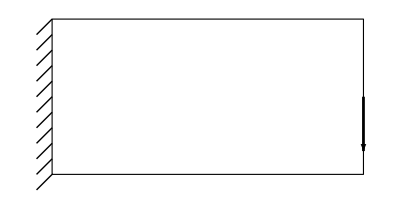
-Graphics- | -Graphics-
-Graphics3D- | -Graphics3D-

```mathematica
imgdata[[1]]
```

```mathematica
ListAnimate[imgdata]
```

```mathematica
Export["C:\\Users\\Andrey\\Desktop\\Conference\\animate.gif",imgdata]
```

C:\Users\Andrey\Desktop\Conference\animate.gif